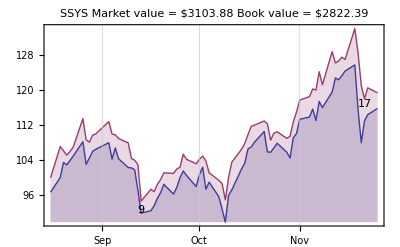

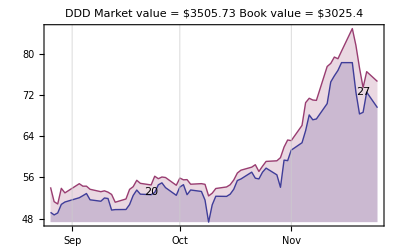

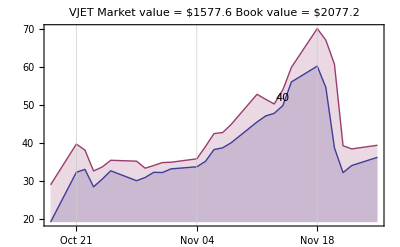

```mathematica
(* FinanceData[] doesn't appear to have Canadian listings: CJR.B, or the symbol is different *)
Clear[ txCanadian ]
txCanadian = {"CJR.B",40,22.500,{2012,7,23,0,0,0}} ;

(* {symbol, shares, price, date} *)
Clear[ tx ]
tx = {
{"SSYS",9,92.750,{2013,9,13, 0}},
{"DDD",20,53.260,{2013,9,23, 0}},
{"VJET",40,51.930,{2013,11,14, 0}},
{"DDD",27,72.600,{2013,11,21, 0}},
{"SSYS",17,116.920,{2013,11,21, 0}}
} ;

(* helper functions *)
ClearAll[ sortTxListByDate ]
sortTxListByDate[l_] := Sort[l, AbsoluteTime[#1[[4]]] < AbsoluteTime[#2[[4]]] &] ;
sortTxListByDate::usage = "In case it becomes convienent to not order the above list by date.  Assuming that Select keeps sort ordering." ;

Clear[ ssys, ddd, vjet ] 
ssys = Select[ tx, #[[1]] == "SSYS" & ] ;
ddd = Select[ tx, #[[1]] == "DDD" & ] ;
vjet = Select[ tx, #[[1]] == "VJET" & ] ; 

(*Module[{nWeeks},
nWeeks = 2 ;
DateListPlot[{#[[4]] - {0, 0, 0, 24*7*nWeeks} , #[[2]]*#[[3]]} &/@ tx,
PlotRange -> Full, PlotLabel -> "Transaction dollar amount"]
]*)

ClearAll[ nShares, bookValue ]
nShares[l_] := Total[l[[All, 2]]] ;
nShares::usage = "Total the number of shares in the given transaction list.  Assumed that the symbol is identical for all in the list." ;
(* correct nomenclature? *)
bookValue[l_] := Sum[ l[[i]][[2]] * l[[i]][[3]], {i, Length[l]} ] ;
bookValue::usage = "sum the initial purchase price times the number of shares for the transactions in the list" ;

historyAndPoints::usage = "Plot high, low for the symbol in the transaction list, and the specifics of those transactions" ;
historyAndPoints[l_] := Module[{oldestTx, n, data, lastClose, ns, bookVal},
oldestTx = l[[1]] ;
n = 4 ; (* include this many weeks data prior to initial purchase *)

data =  FinancialData[ oldestTx[[1]], #,oldestTx[[4]] -{0, 0, 0, 24*7*4}] &/@ {"Low", "High"} ;

lastClose = Last[Last[ Last[ data ] ] ];

ns=nShares[l] ;
bookVal = bookValue[l] ;

DateListPlot[ 
Evaluate@data
, PlotLabel -> Row[{oldestTx[[1]], " Market value = $", ns lastClose, " Book value = $", bookVal }]
, Joined -> True
, Filling->Bottom
, Epilog ->  
Flatten[ Tooltip[
Text[#[[2]],{#[[4]],#[[3]]}]
, Row[{
#[[3]], " ($", #[[2]]*#[[3]]," -> $", #[[2]] * lastClose, ")"
}] 
]&/@ l, 1]
]
]


historyAndPoints[ ssys ]
historyAndPoints[ ddd ]
historyAndPoints[ vjet ]
```